## Лабораторная работа 5

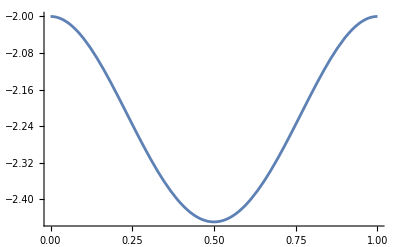
Решить дифференциальное уравнение  y'=πsin(2πx)/y,  y(0)=−2 явным  методом Рунге-Кутта 3 порядка, методом Эйлера с пересчётом  и неявным двухшаговым методом Адамса.
Найдём точное решение:
dy/dx=πsin(2πx)/y,
ydy=πsin(2πx)dx,
∫ydy=∫πsin(2πx)dx=1/2∫sin(2πx)d2πx,
y^2/2=−1/2cos2πx+C,
y^2=−cos2πx+C_1,
y=±√(−cos2πx+C_1),
y(0)=−2<0⇒y=−√(−cos2πx+C_1),
y(0)=−√(−1+C_1)=−2,
−1+C_1=4,
C_1=5,
y(x)=−√(5−cos2πx)
Его график на отрезке [0, 1]:
-Graphics-

## Метод Эйлера с пересчётом

Расчётная формула: -Graphics-
Порядок метода равен 2 ( чисмет 2 часть [1], стр. 10-11).
Ниже приводим код для вычисления решения  явным методом Эйлера:
листинг 1:

Конец листинга 1

## Неявный метод Адамса двухшаговый (Мултона)

Расчётная формула метода: -Graphics-
Исходное уравнение: y'=πsin(2πx)/y.
Подставим в расчётную формулу правую часть ДУ и решим уравнение относительно y_(n+1):
-Graphics-
 Так как начальное условие равно -2, то есть оно отрицательное то при x, близких  к нулю, c будет отрицательно, следовательно √(b^2-4c)>|b|,  откуда (-b-√(b^2-4c))/2<0 и (-b+√(b^2-4c))/2>0, а раз y(0)<0, то - целевая формула для дальнейших вычислений данным методом. Данный метод построен на том, что для него АСТ=3 (так как всего может варьироваться 4 параметра при выводе метода через его равенство для многочленов степени 3 и ниже), значит по утверждению ([1], стр 23) его невязка будет иметь порядок 4. Согласно теореме ([1], стр 26), он будет сходиться с третьим порядком, если он нуль-устойчив и имеет разгон порядка не ниже 3. В качестве разгона воспользуемся методом Рунге кутты третьего порядка. Проверим метод на нуль-устойчивость: y_n=p^n, тогда получим разностное уравнение p^(n+1)=p^n откуда p=1 или p=0, то есть разностное уравнение устойчиво, следовательно, метод нуль-устойчив. Значит по упомянутой теореме метод Адамса Мултона сойдётся с третьим = порядком

## Метод Рунге-Кутты 3его порядка

Расчётная формула: k_1=f(x_n,y_n)
k_2=f(x_n+h,y_n+k_1)
k_3=f(x_n+h/2,y_n+1/4 k_1+1/4 k_2)
y_(n+1)=y_n+h/6(k_1+k_2+4 k_3)
Порядок метода равен 3 ([1] стр. 13).

## В ходе решения получим следующие графики: -Graphics-

## Выводы:

Явные методы сошлись лучше чем неявный метод Адамса-мултона

## Список литературы

Пименов В.Г., Ложников А.Б. Численные методы 2 часть. Екатеринбург: Издательство Уральского университета, 2014.